## README

The following code generates or modifies the images found in the paper as well as creates the JSON file needed in the web app.  Keep in mind that

* code for this section will only work if either pre-computed gaits have been loaded or gaits have been generated in corresponding Main.nb file.

* outputs generated in this section will be placed in 
	** GaitBrowser/src/biped/ for BLExportBipedToThreeJS[...], or 
	** Figures/ for BLExportTo[“Figures”, ...].

* calls to BLBipedTimeGrid assume that a images exist in GaitBrowser/app/imgs.
	** the files already exist, but if you want to regenerate these images, you will need to run the web  app.  You must save the same number of images as BLBipedTimeGrid expects in the “n” argument.  Typically n = 4.

* the code requires installation of an external package: MaTeX.  See "./Installer.nb"../../Installer.nbNone../../Installer.nb in the root directory for more information.

## Load Libraries and Create The Model

## Load Libraries

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[], "../../"}]];
<< "SIMple`";

SetDirectory[FileNameJoin[{NotebookDirectory[], "../"}]];
<< "CompassGait`";
```

## Compile Biped

```mathematica
n = 1;
CompassGait[n]; // AbsoluteTiming
```

{0.164812,Null}

## Load Gaits

```mathematica
BLGetFrom["Here", "cgw.mx"];
```

## Outputs for Paper and Node.js

## Drawings for Paper

### Plot in Figure 5

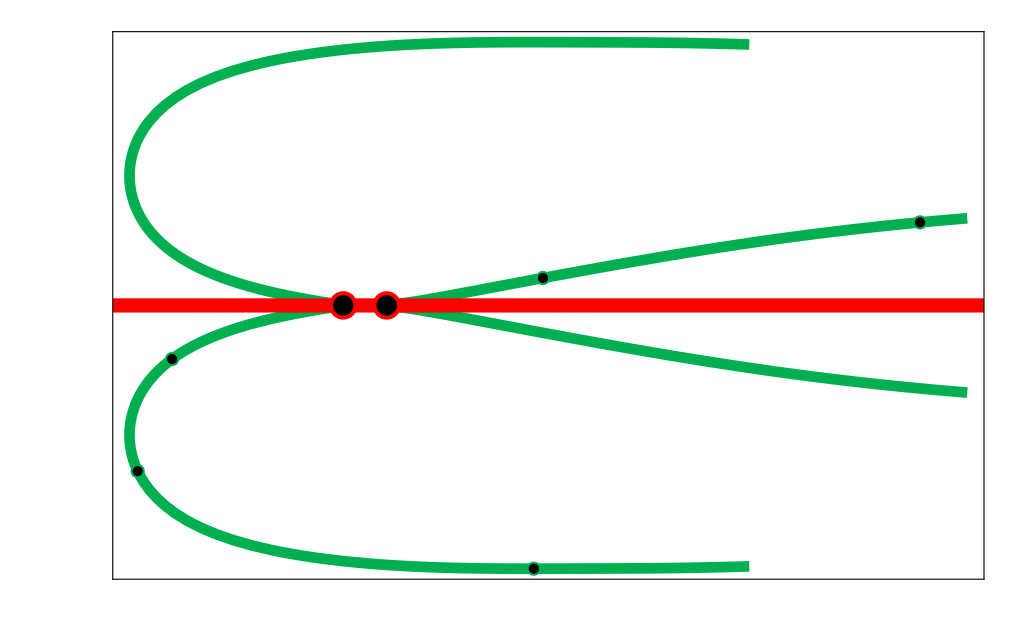

```mathematica
co = <|1 -> <|{-200}-> None, {-140}-> None, {-80}-> None|>, 2 -> <|{105}-> None, {40}-> None|>|>; (* better code would keep keys here and in gaits below in sync *)
ps = 0.5 BipedalLocomotion`Private`EPSize;

BLPlotProjection[man1, man2⟦;;227⟧, Projection -> "z", ListPlot -> {ImageSize -> 72{14.24, 9}}, Callout -> co, PointSize -> {ps, 0.5ps}, Magnification -> {2, 1.5}]

BLExportTo["Figures",  "cgw-cc-path.svg", %];
```

### Gaits in Figures 5

```mathematica
txtbx = {5, 3/4, 1/4};

imgs = "Figure 5(e) - Compass-Gait Walker/*.png";

imgs = BLBipedTimeGrid[man1⟦Key@{-80}, 1⟧, "n" -> Automatic-> 4, ImageSize -> txtbx, ImageData -> imgs, ImageCrop -> False];

BLExportTo["Figures", "cgw-traj-1--80.pdf", imgs];
```

## Node.js (ThreeJS)

Create a JSON file with trajectory and kinematic information for use in GaitBrowser web app

```mathematica
steps = 4;(* 1 for pictures and 4+ for video *)
A = <|
"Model" -> <|
"Figure 5(e) - Compass-Gait Walker" -> BLGaitKinematics[man1⟦Key@{-80}, 1⟧, "n" -> steps],

Options -> CompassGaitMeshOptions[]
|>
|>;
```

```mathematica
BLExportBipedToThreeJS[A];
```